```mathematica
PolyhedronData["Dodecahedron"]
```

-Graphics3D-

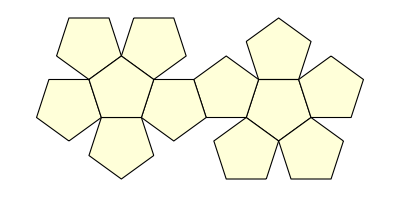

```mathematica
PolyhedronData["Dodecahedron","Net"]
```

```mathematica
PolyhedronData["Cube"]
```

-Graphics3D-

```mathematica
Show[
SphericalPlot3D[1.25,{θ,0,π},{ϕ,0,2π},
RegionFunction->PolyhedronData["Dodecahedron","RegionFunction"],Mesh->None,PlotRange->All,Axes->False],
Graphics3D[{Opacity[0.5],PolyhedronData["Dodecahedron","GraphicsComplex"]}]
]
```

-Graphics3D-

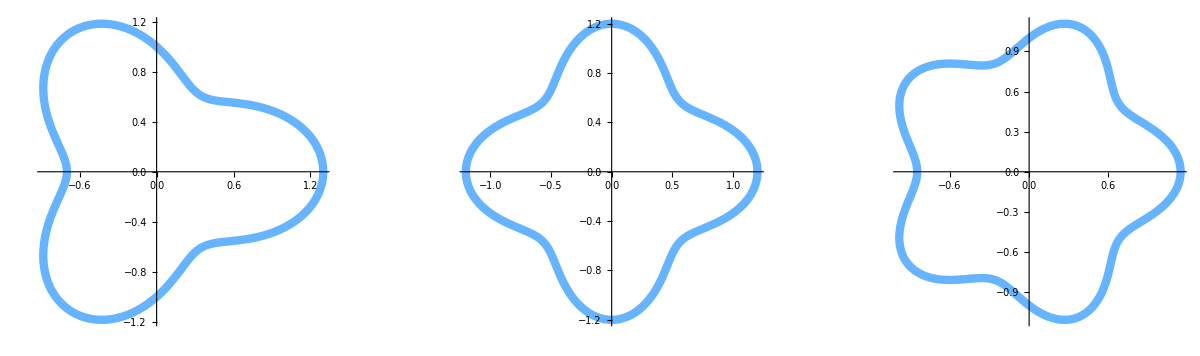

```mathematica
GraphicsRow[MapThread[ParametricPlot[With[{r=1,atd=#1,frq=#2},(r+atd Cos[frq t]) {Cos[t],Sin[t]}],{t,0,2 π},PlotStyle->{RGBColor[0.4,0.7,1],Thickness[0.015]}]&,{{0.3,0.2,0.15},{3,4,5}}],Spacings->Scaled[0.3],ImageSize->Full]
```

```mathematica
GraphicsGrid[Partition[PolyhedronData/@PolyhedronData["Compound"],5]]
```

-Graphics-